```mathematica
f77Values=Import[NotebookDirectory[]<>"../original/result1.txt","Table"]
cppValues=Import[NotebookDirectory[]<>"../clion/cmake-build-debug/out.txt","Table"]
```

{{0.,1.},{0.1,1.005},{0.2,1.02},{0.3,1.045},{0.4,1.08},{0.5,1.125},{0.6,1.18},{0.7,1.245},{0.8,1.32},{0.9,1.405},{1.,1.5}}

{{0,1},{0.1,1.005},{0.2,1.02},{0.3,1.045},{0.4,1.08},{0.5,1.125},{0.6,1.18},{0.7,1.245},{0.8,1.32},{0.9,1.405},{1,1.5}}

```mathematica
f77Values==cppValues
```

True

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

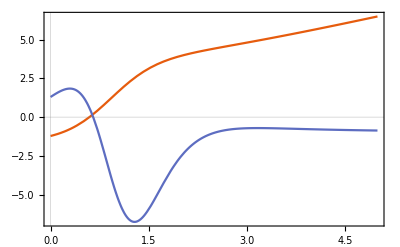

{{6.5,0.902238,-0.864544,7.40224}}

```mathematica
eq={f1''[x]==f2[x]+f1'[x],
0==f2[x]+f1[x]*f1'[x]-x
};
bc={f1[0]==-1.21783702057,f1'[0]==1.067837099200008};
sol=NDSolve[{eq,bc},{f1,f2},{x,0,5}];
psol=Plot[Evaluate[{f1[x],f2[x]}/.sol],{x,0,5},PlotRange->All]
{f1[5],f1'[5],f2[5],f1[5]+f1'[5]}/.sol
```

```mathematica
$PlotTheme="Scientific";
```

{41,3}

{41,3}

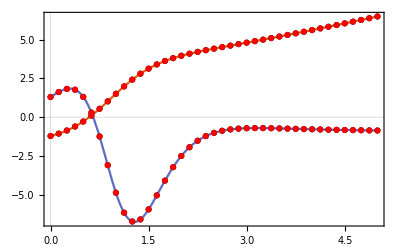

```mathematica
coldaeData=Import[NotebookDirectory[]<>"../original/result_f77.txt","Table"];
coldaeData//Dimensions
coldaeData={coldaeData[[All,{1,2}]],coldaeData[[All,{1,3}]]};

coldaeppData=Import[NotebookDirectory[]<>"../out/x64-Debug/result_cpp.txt","Table"];
coldaeppData//Dimensions
coldaeppData={coldaeppData[[All,{1,2}]],coldaeppData[[All,{1,3}]]};

Show[psol,ListPlot[coldaeData,PlotStyle->Black,Joined->False,PlotRange->All],ListPlot[coldaeppData,PlotStyle->Red]]
```

```mathematica
Interpolation[coldaeData[[1,All]]][0]
Interpolation[coldaeData[[1,All]]]'[0]

Interpolation[coldaeData[[1,All]]][0]+Interpolation[coldaeData[[1,All]]]'[0]
Interpolation[coldaeData[[1,All]]][5]+Interpolation[coldaeData[[1,All]]]'[5]
```

-1.21784

1.06784

-0.15

7.40224

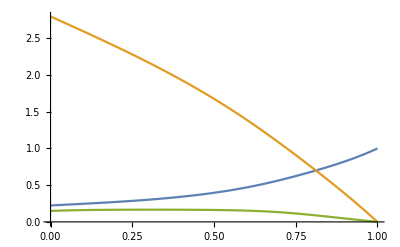

```mathematica
(*Test 4*)
f77Values=Import[NotebookDirectory[]<>"../original/result4.txt","Table"];
ListPlot[{f77Values[[All,{1,2}]],f77Values[[All,{1,4}]],f77Values[[All,{1,6}]]},Joined->True]
```